# Find the GW modes for each planet. Calculate SNR with Bill’s summation over modes and time T (following Maggiore analysis).

## Load the GW functions, mostly from Maggiore chapter 4.

```mathematica
(*Needs["GWFormulae.nb`"]*)
(*Once[ Get["GWFormulae.nb"] ]*)  (* Once insures it is read only once. *)
(*Import["GWFormulae.nb"]*)
thisDir = NotebookDirectory[];
NotebookEvaluate[thisDir<>"GWFormulae.nb"]  (* This works, does spit out the tests and evaluations along the way in the Notebook.  Either comment them out or put up with output. *)
```

The eccentricy and mode dependent power factor called g(n,e) in Maggiore's Eqn. 4.108, note the semi-major axis "a" cancels out of the numerator and denominator.

The frequency in Hz of the binary given the two masses m1, m2, and the semi-major axis a.

Given the exop data table aa and the index to check for blanks filterInd, returns the two lists of non-blank data and black data in that field.

The coefficient in front of the power formulae, especially Maggiore's Eqns. 4.107 (and 4.74).

Given the data table and a string in the header row, returns the header row.  Default string is "pl_hostname" .

```mathematica
?getNmax
```

The approximate mode index n-star where the power curve falls down to 0.05 of the maximum value of the curve.

```mathematica
?fr
```

The frequency of the orbit in Hz given the two masses m1, m2, and the semimajor axis a.

```mathematica
fr[1.0*massE, 1.0*massSun, 1.0*au]*3.1 10^7
```

0.982651

## Read CSV File

```mathematica
thisDir = NotebookDirectory[];
csvDir = thisDir <>"dbases/";
pixDir = thisDir <>"pix/";
csvFileName = csvDir <> "exopP_20180325_114502.csv"
```

/home/gabella/Documents/astro/exop/exoplanetsMath/dbases/exopP_20180325_114502.csv

```mathematica
exopDateTime = dateTimeStamp[csvFileName]
```

20180325_114502

### Grab all the rows in the csv file.

```mathematica
alldata = Import[csvFileName, "Data"];
```

```mathematica
Length[alldata]
```

3707

Test which row has the headers in it, starting at row 1.  Return -999 if there is no element “pl_hostname” at the [[n,1]] position.

```mathematica
rowHeaders = findHeaderRow[alldata]
rowDataStart = rowHeaders+1;
{rowHeaders, rowDataStart}
```

1

{1,2}

### Make the dictionary of column names with createCols[] .

```mathematica
cols = createCols[alldata, rowHeaders]
```

<|pl_hostname→1,pl_letter→2,pl_discmethod→3,pl_orbper→4,pl_orbsmax→5,pl_orbeccen→6,pl_bmassj→7,st_dist→8,st_mass→9,rowupdate→10,st_plx→11|>

```mathematica
{cols["pl_hostname"], cols["st_mass"]}
```

{1,9}

### Filter the data, we need distance, both masses, and the semi-major axis of the orbit to be non-zero for our calculations.

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.

```mathematica
Print["Using database from ", exopDateTime, ".  Length alldata ",Length[alldata] ]
tempdata = alldata;
tempdata= filterBlanks[tempdata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "Number with pl_orbeccen ", Length[tempdata]]
tempdata= filterBlanks[tempdata, cols["pl_orbper"] ][[1]]; Print[ "Number with pl_orbper ",Length[tempdata] ]
tempdata = filterBlanks[tempdata, cols["pl_orbsmax"] ][[1]]; Print["Number with pl_orbsmax ",Length[tempdata] ]
tempdata = filterBlanks[tempdata, cols["pl_bmassj"] ][[1]]; Print["Number with pl_bmassj ",Length[tempdata] ] (* use pl_bmassj not pl_massj *)
tempdata = filterBlanks[tempdata, cols["st_dist"] ][[1]]; Print["Number with st_dist ",Length[tempdata] ]
tempdata = filterBlanks[tempdata, cols["st_mass"] ][[1]]; Print["Number with st_mass ",Length[tempdata] ]
```

Using database from 20180325_114502.  Length alldata 3707

Number with pl_orbeccen 1170

Number with pl_orbper 1170

Number with pl_orbsmax 1105

Number with pl_bmassj 1024

Number with st_dist 918

Number with st_mass 908

```mathematica
?filterBlanks
```

Given the exop data table aa and the index to check for blanks filterInd, returns the two lists of non-blank data and black data in that field.

```mathematica
fdata = tempdata; (* The filtered data. *)
Length[fdata]
```

908

### For each planet build the GW mode set. Interesting to find the highest frequencies with the largest number of modes! The play into the SNR formula best.

Create a data structure with planet row (from filtered data, fdata), eccentricity, and GW mode set.

```mathematica
eccTable = Table[
{icnt,
eccen = fdata[[icnt, cols["pl_orbeccen"] ]], 
nmax = aNmax[ eccen  ];
nmin = aNmin[ eccen ];
Table[
Module[{afreq, plmass, stmass, smax},
plmass = fdata[[icnt, cols["pl_bmassj"]  ]]*massJ;
stmass = fdata[[icnt, cols["st_mass"] ]]*massSun;
smax = fdata[[icnt, cols["pl_orbsmax"]  ]]*au;
afreq = fr[plmass, stmass, smax ];
{pp, pp*afreq, hh [pp,eccen, plmass, stmass, smax,  fdata[[icnt, cols["st_dist"] ]]*pc ]}
], {pp, nmin, nmax}] },
{icnt, 1, Length[fdata]}]
```

{{1,0.53,{{1,5.99455×10^-9,1.87098×10^-26},{2,1.19891×10^-8,2.17487×10^-26},{3,1.79836×10^-8,2.88323×10^-26},{4,2.39782×10^-8,2.66585×10^-26},7,{12,7.19345×10^-8,2.49289×10^-27},{13,7.79291×10^-8,1.75458×10^-27},{14,8.39236×10^-8,1.22948×10^-27},{15,8.99182×10^-8,8.58338×10^-28}}},906,{908,0.04,{1}}}
 |  |  |  |

```mathematica
??chirpM
```

The chirp mass, from Amaro-Seone et al. Eqn. 9.

chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)

```mathematica
?aNmax
```

The maximum useful mode number, 0.05 of the peak of the g(n,e) curve, given an eccentricity.  Care when used for eccentricities above 0.85.

```mathematica
??hh
```

Amaro-Seoane et al.'s dimensionless strain given the mode number, eccentricity, m1, m2, a, and dL the luminosity distance.

hh[n_,e_,m1_,m2_,a_,dL_]:=(bigG^(5/3) 2 √(32/5) chirpM[m1,m2]^(5/3) (2 π fr[m1,m2,a])^(2/3) √gg[n,e])/(cee^4 (n dL))

```mathematica
??massJ
```

Mass of Jupiter in kg.

massJ=1.9×10^27

```mathematica
?massSun
```

Mass of the sun in kg.

```mathematica
?au
```

Astronomical units in meters.

### Make a plot of all the modes versus frequency, like I have done in the past.

```mathematica
getModesOnly[eccTable_, row_]:=Module[{aa,bb},
aa = eccTable[[row,3]]; (* The list of modes with mode number {{1, 5.999e-9, 1.87e-26},{2, ...} } *)
Table[
{aa[[ii,2]], aa[[ii,3]]},
{ii,1,Length[aa]}]
]
```

```mathematica
getModesOnly[eccTable,1]
```

{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27},{8.99182×10^-8,8.58338×10^-28}}

```mathematica
allEccList = Table[
getModesOnly[eccTable,ii],
{ii, 1, Length[eccTable]}];
```

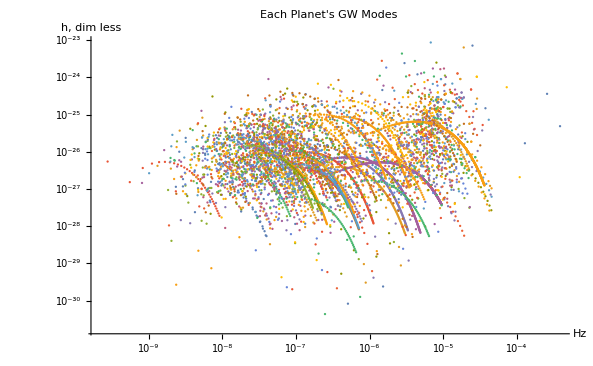

```mathematica
ListLogLogPlot[allEccList,
PlotLabel->"Each Planet's GW Modes",
AxesLabel->{"Hz", "h, dim less"}
]
```

## Plot e vs f_orb, for detection want high eccentricity but also high orbital frequency.

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
(* orbital period is in days *)
listEvF = Table[
{1.0/(fdata[[ii, cols["pl_orbper"] ]]*24.0*3600.0),fdata[[ii, cols["pl_orbeccen"] ]]},
{ii, 1, Length[fdata]}];
```

```mathematica
{Length[listEvF]}
```

{908}

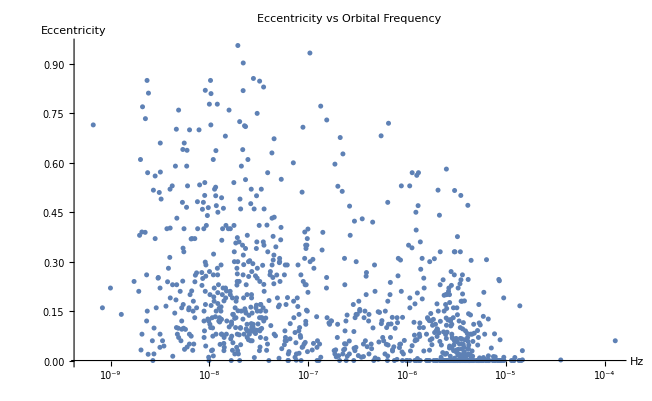

```mathematica
ListLogLinearPlot[listEvF,
PlotLabel->"Eccentricity vs Orbital Frequency",
AxesLabel->{"Hz", "Eccentricity"}
]
```

### Plot Nmax(e) vs Frequency

```mathematica
listNvF = Table[
{1.0/(fdata[[ii, cols["pl_orbper"] ]]*24.0*3600.0),aNmax[ fdata[[ii, cols["pl_orbeccen"] ]] ] },
{ii, 1, Length[fdata]}];
Length[listNvF]
```

908

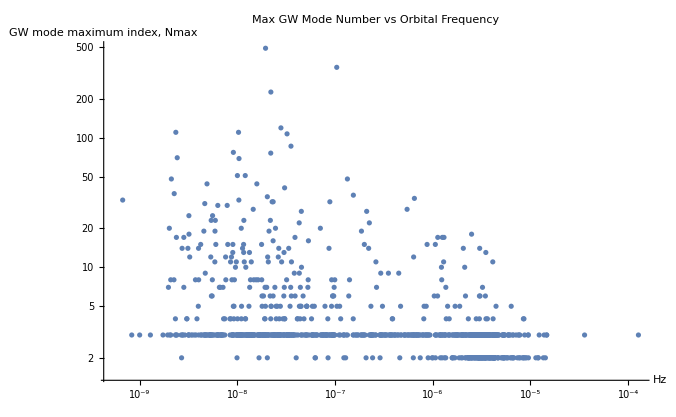

```mathematica
ListLogLogPlot[listNvF,
PlotLabel->"Max GW Mode Number vs Orbital Frequency",
AxesLabel->{"Hz", "GW mode maximum index, Nmax"}
]
```

## S_n(f) for frequency below few mHz.

```mathematica
(*<<MaTeX`*)
```

```mathematica
(* Larson formula for now. *)
ssubn[freq_]:=0.1642*10^-48/freq^4
```

Actually the fit in the python notebook for the left hand side of the S_n(f) from Larson’s Sqrt[S_n(f)] was TeXForm[f^-3.9946\cdot 1.6421 \cdot 10^-49]  .

```mathematica
{10^(-48.7846), 10^(-48.7846+49)}
```

{1.6421×10^-49,1.6421}

I used Larson’s site at CalTech to make two sensitivity curves, both per root Hz (ASD), and python/scg_4728.dat has 30 cm optics, 1 W, and 1e9 m arm length, while to match the GOAT report python/scg_5597_2W_2p5e9m.dat has 30 cm optics, 2 W, and 2.5e9 m arm length.  See Fig. 1 and text below that in GOAT report:  Danzman et al., LISA L3, 20170120.

```mathematica
(*larsonFileName = "python/scg_4728.dat";*)
larsonFileName = thisDir<>"python//scg_5597_2W_2p5e9m.dat";
larsonTot = Import[larsonFileName];
Length[larsonTot]
larsonTot[[1;;23]]//MatrixForm  (* Especially Curve Type being Root Spectral Density, per root Hz...the Amplitude Spectral Density. *)
```

922

({#,Code:,cgiSensePlot.c,v4.0,(sll,-,13,February,2009,Build)}
{#,from,WWW,Sensitivity,Curve,Generator,located,at:}
{#,http://www.srl.caltech.edu/~shane/sensitivity/MakeCurve.html}
{#,EQUAL,ARM,Space,Based,Observatory,Sensitivity,Curve}
{#,Polarization,and,All,Sky,Averaged}
{#}
{#,For,this,data,file:}
{#,SNR,=,1.}
{#,Armlength,=,2.5×10^9,meters}
{#,Optics,diameter,=,0.3,meters}
{#,Wavelength,=,1064.,nanometers}
{#,Laser,power,=,2.,Watts}
{#,Optical,train,efficiency,=,0.3}
{#,Accleration,noise,=,3.×10^-15,m/(s^2,root,Hz)}
{#,Position,noise,=,2.×10^-11,m/(root,Hz)}
{#,Sensitivity,Floor,Set,by,Position,Noise,Budget}
{#,Output,Curve,type,is,Root,Spectral,Density,,per,root,Hz}
{#,Astrophysical,Noise,is,No,White,Dwarf,Noise}
{#}
{#}
{#}
{#,f,[Hz],hf,[Hz^(-1/2)]}
{1.95301×10^-7,4.11527×10^-12})

See Text above, using two data files from Larson both ASDs.
GOAT report Fig. 1 uses (and maybe Fig. 2) L=2.5e9 m, optics 30cm and 2W.  Above is different than that, L=1.0e9 m and 1 W.

```mathematica
larsonData = Module[{aa,bb},
aa={};
Table[
If[larsonTot[[ii,1]]=="#",,
aa~AppendTo~larsonTot[[ii]];
],
{ii, 1, Length[larsonTot]}  ];(* end Table *)
aa
];
Length[larsonData]
```

900

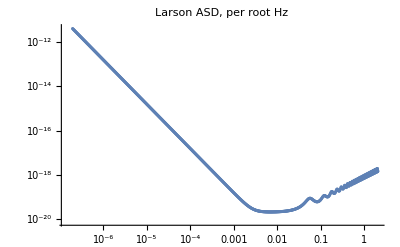

```mathematica
ListLogLogPlot[larsonData,
PlotLabel->"Larson ASD, per root Hz",
PlotTheme->Grid (*,
PlotRange->{10^-20, 10^-19}*)
]
```

```mathematica
larsonSn = Module[{aa,bb},
{aa, bb} = Transpose[larsonData];
Transpose[{aa, bb^2}]
];
Length[larsonSn]
```

900

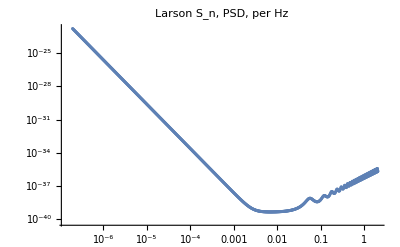

```mathematica
ListLogLogPlot[larsonSn,
PlotLabel->"Larson S_n, PSD, per Hz",
PlotTheme->Grid
]
```

Fit the part from 2e-3 Hz to all the way to the left.  Did this in Python notebook, see results below.

```mathematica
larsonSn[[1;;2]]
larsonSn[[1,1]]
```

{{1.95301×10^-7,1.69354×10^-23},{1.99851×10^-7,1.54449×10^-23}}

1.95301×10^-7

```mathematica
fitLarsonSn = Module[{aa,bb},
aa={};
Table[
If[larsonSn[[ii,1]]<=2 10^-3,
aa~AppendTo~larsonSn[[ii]]  ],
{ii, 1, Length[larsonSn]}];
aa];
Length[fitLarsonSn]
```

401

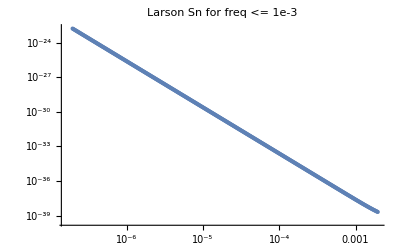

```mathematica
aplot=ListLogLogPlot[ fitLarsonSn,
PlotLabel->"Larson Sn for freq <= 1e-3",
PlotTheme->"Grid"
]
```

```mathematica
larsonSnFit = Fit[  Log10@fitLarsonSn, {1,u}, u]  (* Fit a line to the Log10 of the data. *)
```

-49.5861-3.99588 u

```mathematica
larsonSnFitB = NonlinearModelFit[  fitLarsonSn, a*f^b, {{a,10^-49},{b,-4}},f]  (* Fit a nonlinear function of the data. *)
```

FittedModel[(2.46386×10^-50)/f^4.]

```mathematica
Normal[larsonSnFitB]
```

(2.46386×10^-50)/f^4.

```mathematica
larsonSnFitB[10^-5]
```

2.46385×10^-30

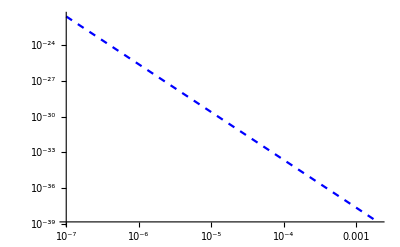

```mathematica
bplot =  LogLogPlot[larsonSnFitB[f],{f, 10^-7, 2 10^-3},
PlotStyle->{RGBColor[{0,0,1}], Dashed}]
```

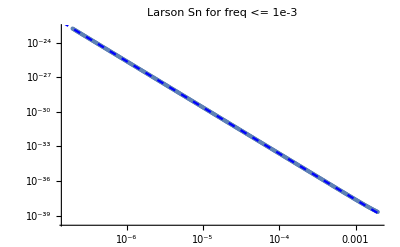

```mathematica
Show[{aplot,bplot}  ]
```

Using the same data file as Python notebook scg_4728.dat, the linear fit of the Log10 data is -48.7846 - 3.99458 Log10[f] here and in Python it was -48.7846-3.9946 Log10[f] .  Okay that is pretty good, if not identical.
NOW, use the 2.5e9 m 2W file!  scg_5597_2W_2p5e9m.dat.

2W 2p5e9m arm length fit is -49.5861 - 3.99588 Log10[f] .

```mathematica
aa=larsonSnFit/.u->Log10[10^-5]
10^aa
```

-29.6067

2.47359×10^-30

```mathematica
larsonSnFit/.u->10^-5
```

-49.5861

```mathematica
ssubnFit[u_]:=10^#1 x^#2 &
```

## Signal-to-Noise following Bill’s formula

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
getModesOnly[ eccTable, 1 ]
```

{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27},{8.99182×10^-8,8.58338×10^-28}}

```mathematica
intTime = 1.0*secsYear; (* integration time in seconds *)
SNRTable= Table[
{fdata[[ii,cols["pl_hostname"] ]]<>" "<>fdata[[ii,cols["pl_letter"] ]],
fdata[[ii, cols["pl_orbeccen"] ]], fdata[[ii, cols["pl_orbper"] ]],
Sqrt[
Module[{aa, bb},
If[Length[eccTable[[ii]] ]==1,
aa=getModesOnly[ eccTable, ii ][[1,1]];(* freq Hz *)
bb = getModesOnly[ eccTable, ii][[1, 2]];(* h dim less *)
intTime*bb^2/(2.0*ssubn[aa]),
Sum[
aa=getModesOnly[ eccTable, ii ][[jj,1]];(* freq Hz *)
bb = getModesOnly[ eccTable, ii][[jj, 2]];(* h dim less *)
intTime*bb^2/(2.0*ssubn[aa]),
{jj, 1, Length[  getModesOnly[eccTable, ii]  ] } ]
](* end IF *)
](* end Module *)
],(* end Sqrt *)
ii},
{ii, 1, Length[eccTable]}  ];
```

Order is Star and Planet name, eccentricity, orbital period in days, SNR, index in fdata table.

```mathematica
SNRTable[[1]]
```

{HD 142022 A b,0.53,1928.,5.84207×10^-13,1}

```mathematica
Length/@{eccTable, fdata, SNRTable}
```

{908,908,908}

```mathematica
SNRTableSorted = Sort[SNRTable, #1[[4]]> #2[[4]] &];
```

```mathematica
SNRTableSorted[[1;;10]]//TableForm
```

PSR J1719-1438 b | 0.06 | 0.0907063 | 0.00024401 | 331
WASP-18 b | 0.0092 | 0.941453 | 0.0000436513 | 121
PSR J2322-2650 b | 0.0017 | 0.322964 | 0.0000281842 | 233
KELT-1 b | 0.0099 | 1.21751 | 0.0000224982 | 737
WASP-43 b | 0. | 0.813475 | 8.31036×10^-6 | 368
tau Boo b | 0.011 | 3.31246 | 3.89922×10^-6 | 577
KELT-9 b | 0. | 1.48112 | 3.04021×10^-6 | 739
KELT-16 b | 0. | 0.968995 | 2.63242×10^-6 | 686
WASP-77 A b | 0. | 1.36003 | 2.57176×10^-6 | 392
WASP-19 b | 0.002 | 0.788839 | 2.18948×10^-6 | 122

```mathematica
{1/(0.0907063*secsDay),ssubn[1/(0.0907063*secsDay)]}
```

{0.000127599,6.1941×10^-34}

```mathematica
ordTable={{"name", "eccen", "orb per, days", "SNR", "fdata index"}}~Join~SNRTableSorted[[1;;10]]//TableForm
```

name | eccen | orb per, days | SNR | fdata index
PSR J1719-1438 b | 0.06 | 0.0907063 | 0.00024401 | 331
WASP-18 b | 0.0092 | 0.941453 | 0.0000436513 | 121
PSR J2322-2650 b | 0.0017 | 0.322964 | 0.0000281842 | 233
KELT-1 b | 0.0099 | 1.21751 | 0.0000224982 | 737
WASP-43 b | 0. | 0.813475 | 8.31036×10^-6 | 368
tau Boo b | 0.011 | 3.31246 | 3.89922×10^-6 | 577
KELT-9 b | 0. | 1.48112 | 3.04021×10^-6 | 739
KELT-16 b | 0. | 0.968995 | 2.63242×10^-6 | 686
WASP-77 A b | 0. | 1.36003 | 2.57176×10^-6 | 392
WASP-19 b | 0.002 | 0.788839 | 2.18948×10^-6 | 122

```mathematica
Export[thisDir<>"tableSNR.txt", ordTable]
```

/home/gabella/Documents/astro/exop/exoplanetsMath/tableSNR.txt

```mathematica
ordTable2={{"name", "eccen", "orb per, days", "SNR", "fdata index"}}~Join~SNRTableSorted[[1;;10]]
```

{{name,eccen,orb per, days,SNR,fdata index},{PSR J1719-1438 b,0.06,0.0907063,0.00024401,331},{WASP-18 b,0.0092,0.941453,0.0000436513,121},{PSR J2322-2650 b,0.0017,0.322964,0.0000281842,233},{KELT-1 b,0.0099,1.21751,0.0000224982,737},{WASP-43 b,0.,0.813475,8.31036×10^-6,368},{tau Boo b,0.011,3.31246,3.89922×10^-6,577},{KELT-9 b,0.,1.48112,3.04021×10^-6,739},{KELT-16 b,0.,0.968995,2.63242×10^-6,686},{WASP-77 A b,0.,1.36003,2.57176×10^-6,392},{WASP-19 b,0.002,0.788839,2.18948×10^-6,122}}

```mathematica
Export[thisDir<>"tableSNR2.txt", ordTable2]
```

/home/gabella/Documents/astro/exop/exoplanetsMath/tableSNR2.txt

```mathematica
Export[thisDir<>"tableSNR2.tex", ordTable2]
```

/home/gabella/Documents/astro/exop/exoplanetsMath/tableSNR2.tex